```mathematica
EulerCauchy[df1_,h_,xn_,yn_,steps_]:=Block[{vecresp,y,x,i,x0,v0,x1,v1,t=yn},
vecresp=Table[0,{steps},{2}];
v0=xn;
x0=yn;
For[i=1,i≤steps,i++,
v1=v0+h df1[x0];
x1=x0+v0 h;
v0=v1;
x0=x1;
t+=h;
vecresp[[i,1]]=t;
vecresp[[i,2]]=v0;
];
Return[vecresp];
]
```

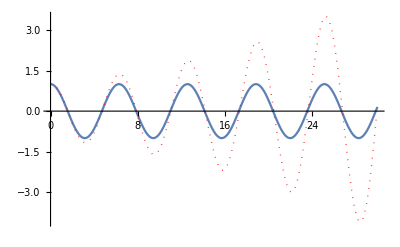

```mathematica
df1[x_]:=-x;
h=0.1;
sol=EulerCauchy[df1,h,1,0,30/h];
a=Plot[Cos[t],{t,0,30}];
b=ListLinePlot[sol,PlotStyle->{Thick,Dotted,Red}];
Show[a,b,PlotRange->All]
```

```mathematica
EulerCauchy[df1_,Δt_,vn_,xn_,steps_]:=Block[{vecresp,y,x,i,x0,v0,x1,v1,t},
vecresp=Table[0,{steps},{2}];
v0=vn;
x0=xn;
t=0;
For[i=1,i≤steps,i++,
v1=v0+Δt df1[x0];
x1=x0+v0 Δt;
vecresp[[i,1]]=x0;
vecresp[[i,2]]=v0;
v0=v1;
x0=x1;
t+=Δt;
];
Return[vecresp];
]
```

```mathematica
Clear[MM,k]
solanalytic=DSolve[{x''[t]==- k/MM x[t],x[0]==1,x'[0]==0},x[t],t][[1,1,2]]
```

Cos[(√k t)/(√MM)]

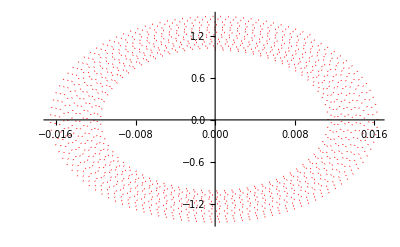

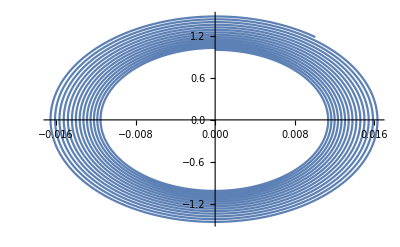

```mathematica
k=15708.;
MM=2.;
df1[x_]:=-k/MM x;
Δt=0.0001;
ttotal=1;
vn=1.;
xn=0.;
sol=EulerCauchy[df1,Δt,vn,xn,ttotal/Δt];
a=Plot[solanalytic,{t,0,ttotal}];
b=ListLinePlot[sol,PlotStyle->{Thick,Dotted,Red}]
ListLinePlot[sol]
Show[a,b,PlotRange->All];
```

```mathematica
EulerCauchyBeam[M_,h_,θn_,un_,steps_]:=Block[{vecresp,y,x,i,x0,v0,x1,v1,u,u0,θ,θ0},
vecresp=Table[0,{steps},{2}];
θ0=θn;
u0=un;
x0=0.;
For[i=1,i≤steps,i++,
θ=θ0+h M[x0];
u=u0+h θ0;

vecresp[[i,1]]=x0;
vecresp[[i,2]]=u0;
θ0=θ;
u0=u;
x0+=h;

(*If[i≠steps,
vecresp[[i,1]]=x0;
vecresp[[i,2]]=u0;
θ0=θ;
u0=u;
x0+=h;
,
θ0=θ;
u0=u;,
x0+=h;
vecresp[[i,1]]=x0;
vecresp[[i,2]]=u0;
];*)
];

Return[vecresp];
]
```

```mathematica
L=5;
ei=2.1 10^8 (0.1 0.2^3)/12
q=20
m=q L x/2 - q x x/2;
soleqviga=DSolve[{u''[x]==m/ ei,u[0]==0,u[L]==0},u[x],x][[1,1,2]]
```

14000.

20

-0.00744048 x+0.000595238 x^3-0.0000595238 x^4

```mathematica
D[soleqviga,x]/.x->0
```

-0.00744048

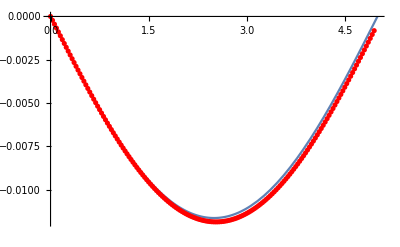

```mathematica
M[x_]:=(q L x/2 - q x x/2)/ei;
h=0.03;
θn=D[soleqviga,x]/.x->0;
un=0;
sol=EulerCauchyBeam[M,h,θn,un,L/h];

a=Plot[soleqviga,{x,0,L}];
b=ListPlot[sol,PlotStyle->{Thick,Dotted,Red}];
Show[a,b,PlotRange->All]
```

```mathematica
sol[[Length[sol]]][[2]]
```

-0.000819489

```mathematica
Shoting[M_,h_,un_,steps_]:=Block[{θ=-Pi/2,n=100,dt,soln1,soln,lastsol},
dt=0.5Pi/n;
For[i=1,i<2n,i++,
sol=EulerCauchyBeam[M,h,θ,un,steps];
θ+=dt;
lastsol=sol[[Length[sol]]][[2]];
If[Sign[lastsol]>0,

dt*=0.5;
i=1;
n=n 2;
θ=-n dt;
];
If[n>10000,Break[]];

];
Print["u = ",lastsol];
Print["θ = ",θ];
]
```

```mathematica
Sign[5]
```

1

```mathematica
Shoting[M,h,un,L/h]
```

u = 0.000778397

θ = -1.5708

```mathematica
θn=D[soleqviga,x]/.x->0
```

-0.00744048

```mathematica
Exp[3.]
```

20.0855

14000.

10

-125+50 x-5 x^2

-0.00446429 x^2+0.000595238 x^3-0.0000297619 x^4

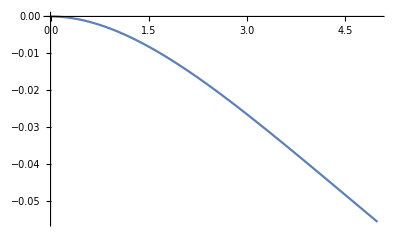

```mathematica
L=5;
ei=2.1 10^8 (0.1 0.2^3)/12
q=10
m=-(L^2 q)/2+L q x-(q x^2)/2
soleqviga=DSolve[{u''[x]==m/ ei,u[0]==0,u'[0]==0},u[x],x][[1,1,2]]
a=Plot[soleqviga,{x,0,L}]
```

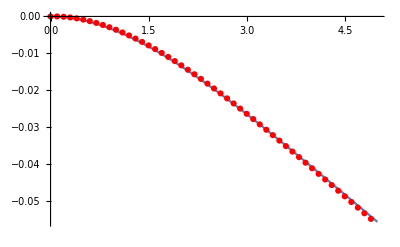

```mathematica
M[x_]:=(-(L^2 q)/2+L q x-(q x^2)/2)/ei
h=0.1;
θn=0;
un=0;
sol=EulerCauchyBeam[M,h,θn,un,L/h];
a=Plot[soleqviga,{x,0,L}];
b=ListPlot[sol,PlotStyle->{Thick,Dotted,Red}];
Show[a,b,PlotRange->All]
```

```mathematica
L
```

5

```mathematica
EulerCauchyBeam[M_,h_,θn_,un_,steps_]:=Block[{vecresp,y,x,i,x0,v0,x1,v1,u,u0,θ,θ0},
vecresp=Table[0,{steps+1},{2}];
θ0=θn;
u0=un;
x0=0.;
θ0=(M[x0+h]-M[x0])/h;
For[i=1,i≤steps,i++,
θ=θ0+h M[x0];
u=u0+h θ0;
vecresp[[i,1]]=x0;
vecresp[[i,2]]=u0;
θ0=θ;
u0=u;
x0+=h;
];
Return[vecresp];
]
```

```mathematica
int=Integrate[M[x],x]
```

0.00178571 x^2-0.000238095 x^3

```mathematica
-(M[0.+0.001]-M[0.])/0.001
```

-0.00357071

```mathematica
D[soleqviga,x]/.x->0
```

-0.00744048

```mathematica
(int/.x->0.001)/0.001
```

1.78548×10^-6

```mathematica
θn=D[soleqviga,x]/.x->0
```

-0.00744048

```mathematica
M[x_]:=(q L x/2 - q x x/2)/ei;
h=0.03;
θn=D[soleqviga,x]/.x->0;
un=0;
L/h
sol=EulerCauchyBeam[M,h,-0.01,un,L/h]
```

166.667

{{0.,0},{0.03,0.0001065},{0.06,0.000213},{0.09,0.000319596},{0.12,0.000426382},{0.15,0.000533453},{0.18,0.0006409},{0.21,0.000748814},{0.24,0.000857287},{0.27,0.000966406},{0.3,0.00107626},{0.33,0.00118693},{0.36,0.00129851},{0.39,0.00141109},{0.42,0.00152473},{0.45,0.00163953},{0.48,0.00175557},{0.51,0.00187292},{0.54,0.00199167},{0.57,0.00211189},{0.6,0.00223366},{0.63,0.00235705},{0.66,0.00248214},{0.69,0.002609},{0.72,0.0027377},{0.75,0.00286832},{0.78,0.00300091},{0.81,0.00313555},{0.84,0.00327231},{0.87,0.00341125},{0.9,0.00355244},{0.93,0.00369594},{0.96,0.00384181},{0.99,0.00399011},{1.02,0.0041409},{1.05,0.00429425},{1.08,0.00445021},{1.11,0.00460883},{1.14,0.00477018},{1.17,0.0049343},{1.2,0.00510125},{1.23,0.00527108},{1.26,0.00544384},{1.29,0.00561958},{1.32,0.00579835},{1.35,0.0059802},{1.38,0.00616517},{1.41,0.00635331},{1.44,0.00654466},{1.47,0.00673927},{1.5,0.00693717},{1.53,0.00713841},{1.56,0.00734302},{1.59,0.00755104},{1.62,0.00776252},{1.65,0.00797748},{1.68,0.00819595},{1.71,0.00841799},{1.74,0.00864361},{1.77,0.00887284},{1.8,0.00910572},{1.83,0.00934228},{1.86,0.00958254},{1.89,0.00982653},{1.92,0.0100743},{1.95,0.0103258},{1.98,0.0105811},{2.01,0.0108403},{2.04,0.0111033},{2.07,0.0113701},{2.1,0.0116409},{2.13,0.0119155},{2.16,0.012194},{2.19,0.0124765},{2.22,0.0127629},{2.25,0.0130533},{2.28,0.0133477},{2.31,0.013646},{2.34,0.0139483},{2.37,0.0142546},{2.4,0.0145649},{2.43,0.0148792},{2.46,0.0151976},{2.49,0.0155199},{2.52,0.0158463},{2.55,0.0161766},{2.58,0.016511},{2.61,0.0168494},{2.64,0.0171919},{2.67,0.0175383},{2.7,0.0178887},{2.73,0.0182432},{2.76,0.0186016},{2.79,0.018964},{2.82,0.0193304},{2.85,0.0197008},{2.88,0.0200751},{2.91,0.0204533},{2.94,0.0208355},{2.97,0.0212216},{3.,0.0216115},{3.03,0.0220054},{3.06,0.0224031},{3.09,0.0228046},{3.12,0.02321},{3.15,0.0236191},{3.18,0.0240321},{3.21,0.0244487},{3.24,0.0248691},{3.27,0.0252932},{3.3,0.0257209},{3.33,0.0261523},{3.36,0.0265873},{3.39,0.0270259},{3.42,0.027468},{3.45,0.0279136},{3.48,0.0283627},{3.51,0.0288152},{3.54,0.0292712},{3.57,0.0297305},{3.6,0.0301931},{3.63,0.030659},{3.66,0.0311281},{3.69,0.0316005},{3.72,0.0320759},{3.75,0.0325545},{3.78,0.0330362},{3.81,0.0335209},{3.84,0.0340085},{3.87,0.034499},{3.9,0.0349924},{3.93,0.0354887},{3.96,0.0359877},{3.99,0.0364893},{4.02,0.0369937},{4.05,0.0375006},{4.08,0.03801},{4.11,0.038522},{4.14,0.0390363},{4.17,0.039553},{4.2,0.040072},{4.23,0.0405932},{4.26,0.0411166},{4.29,0.041642},{4.32,0.0421695},{4.35,0.042699},{4.38,0.0432303},{4.41,0.0437634},{4.44,0.0442983},{4.47,0.0448349},{4.5,0.0453731},{4.53,0.0459128},{4.56,0.0464539},{4.59,0.0469964},{4.62,0.0475402},{4.65,0.0480852},{4.68,0.0486313},{4.71,0.0491785},{4.74,0.0497267},{4.77,0.0502757},{4.8,0.0508255},{4.83,0.051376},{4.86,0.0519272},{4.89,0.0524788},{4.92,0.0530309},{4.95,0.0535834},{0,0}}